#### FWHM of X - ray pulse

```mathematica
FWHM==Sqrt[2 Log[2]]σ
```

FWHM==σ √(2 Log[2])

```mathematica
σ=N[FWHM/(2Sqrt[2 Log[2]])]/.FWHM->1 10^-6(*in meters*)
```

4.24661×10^-7

```mathematica
σ=(1.5 10^-6)/2.355
```

6.36943×10^-7

#### X - ray intensity distribution

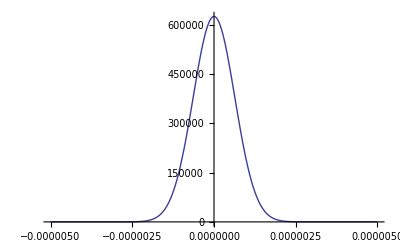

```mathematica
Plot[PDF[NormalDistribution[0,σ] ,x],{x,-5 10^-6,5 10^-6}]
```

```mathematica
numberOfPhotons=10^12 *0.2 (*AMO beamline transmission*);
```

```mathematica
NIntegrate[ numberOfPhotons PDF[NormalDistribution[0,σ] ,x],{x,-5 10^-6,5 10^-6}]
```

2.×10^11

```mathematica
NIntegrate[numberOfPhotons PDF[NormalDistribution[0,σ] ,x],{x,-25 10^-9,25 10^-9}](*number of photons in LCLS pulse interacting with Xe-cluster*)
```

6.26179×10^9

```mathematica
numberOfXrayPhotonsInSample=NIntegrate[numberOfPhotons PDF[BinormalDistribution[{σ,σ},0] ,{x,y}],{x,-25 10^-9,25 10^-9},{y,-25 10^-9,25 10^-9}]
```

1.9605×10^8

```mathematica
crossSectionOfXeAtom=3 10^-18;(*in cm^2*)
```

```mathematica
numberOfAbsorbedPhotons=(numberOfXrayPhotonsInSample*crossSectionOfXeAtom)/(625 10^-14(*in cm^2*)) (*units???*)
```

94.1039

```mathematica
eVinXray=numberOfAbsorbedPhotons*837(*absorbed X-ray energy in eV*)
```

78765.

#### IR intensity distribution

```mathematica
σIR=(40 10^-6)/2.355
```

0.0000169851

```mathematica
intensityIR=2 10^15 (*watt cm^-2*);
```

```mathematica
pulseLengthIR = 70 10^-15 (*seconds*);
```

```mathematica
photonEnergy=1.5 (*electronvolt*)*1.60218 10^-19(*in Joule*)
```

2.40327×10^-19

```mathematica
ConversionCMfocusToμm=1600 10^-8 (*focus is 1600 μm^2, so this is in cm^2*)
```

1/62500

```mathematica
numberOfIRphotons=intensityIR/photonEnergy pulseLengthIR *ConversionCMfocusToμm
```

9.32063×10^15

```mathematica
(numberOfIRphotons *photonEnergy)/pulseLengthIR(*sanity check watt cm^-2*)
```

3.2×10^10

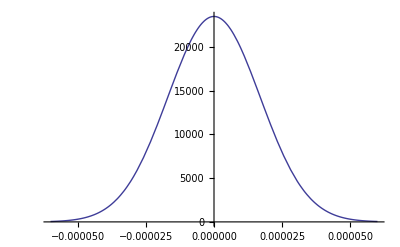

```mathematica
Plot[PDF[NormalDistribution[0,σIR] ,x],{x,-60 10^-6,60 10^-6}]
```

```mathematica
NIntegrate[PDF[BinormalDistribution[{σIR,σIR},0] ,{x,y}],{x,-100 10^-6,100 10^-6},{y,-100 10^-6,100 10^-6}]
```

1.

```mathematica
Plot3D[PDF[BinormalDistribution[{σIR,σIR},0] ,{x,y}],{x,-100 10^-6,100 10^-6},{y,-100 10^-6,100 10^-6}]
```

-Graphics3D-

```mathematica
numberOfIRphotonsInSample=NIntegrate[numberOfIRphotons PDF[BinormalDistribution[{σIR,σIR},0] ,{x,y}],{x,-25 10^-9,25 10^-9},{y,-25 10^-9,25 10^-9}]
```

1.28549×10^10

```mathematica
NIntegrate[PDF[NormalDistribution[0,σIR] ,x],{x,-100 10^-6,100 10^-6}]
```

1.

```mathematica
NIntegrate[ numberOfIRphotons PDF[NormalDistribution[0,σIR] ,x],{x,-5 10^-6,5 10^-6}]
```

2.15799×10^15

```mathematica
NIntegrate[numberOfIRphotons PDF[NormalDistribution[0,σIR] ,x],{x,-25 10^-9,25 10^-9}](*number of photons in LCLS pulse interacting with Xe-cluster*)
```

1.0946×10^13

```mathematica
crossSectionOfXeAtomIR=0.3(*in 10^20 m^2*);
```

```mathematica
crossSectionOfXeAtomIR=30 10^-18;(*in cm^2*)
```

```mathematica
numberOfAbsorbedPhotonsIR=(numberOfIRphotonsInSample*crossSectionOfXeAtomIR)/(625 10^-14(*in cm^2*))(*photons*)
```

61703.3

```mathematica
eVinIR=numberOfAbsorbedPhotonsIR*1.5(*absorbed IR energy in eV*)
```

92554.9

```mathematica
eVinXray/eVinIR
```

0.851008

```mathematica
125/200//N
```

0.625